# Greens functions for quadratic slip on a horizontal fault in antiplane geometry

```mathematica
Get["/Users/mallick/Documents/GitHub/mathematica2matlab/ToMatlab.m"]
Get["/Users/mallickrishg/Downloads/mathematica2matlab/mathematica2matlab/ToMatlab.m"]
```

Get::noopen: Cannot open /Users/mallick/Documents/GitHub/mathematica2matlab/ToMatlab.m.

$Failed

## Point source slip Greens functions

```mathematica
r = Sqrt[(x-xs)^2 +(y-ys)^2];
Upt =1/2/Pi*(y-ys)/r^2
expt = D[Upt,x]
eypt = D[Upt,y]
```

(y-ys)/(2 π ((x-xs)^2+(y-ys)^2))

-((x-xs) (y-ys))/(π ((x-xs)^2+(y-ys)^2)^2)

1/(2 π ((x-xs)^2+(y-ys)^2))-(y-ys)^2/(π ((x-xs)^2+(y-ys)^2)^2)

## Write out 3 quadratic basis functions

```mathematica
Fb1 = xs*(9*xs/(8*a) - 3/4)/a
Fb2 = (1-3*xs/(2*a))*(1+3*xs/(2*a))
Fb3 = xs*(9*xs/(8*a) + 3/4)/a
```

(xs (-3/4+(9 xs)/(8 a)))/a

(1-(3 xs)/(2 a)) (1+(3 xs)/(2 a))

(xs (3/4+(9 xs)/(8 a)))/a

## Integrate/convolve point source with each basis function

### Displacement

```mathematica
u1indef = Integrate[Upt*Fb1,xs,GeneratedParameters->C];
u2indef = Integrate[Upt*Fb2,xs,GeneratedParameters->C];
u3indef = Integrate[Upt*Fb3,xs,GeneratedParameters->C];
```

### Strain

```mathematica
ex1indef = Integrate[expt*Fb1,xs,GeneratedParameters->C];
ex2indef = Integrate[expt*Fb2,xs,GeneratedParameters->C];
ex3indef = Integrate[expt*Fb3,xs,GeneratedParameters->C];
ey1indef = Integrate[eypt*Fb1,xs,GeneratedParameters->C];
ey2indef = Integrate[eypt*Fb2,xs,GeneratedParameters->C];
ey3indef = Integrate[eypt*Fb3,xs,GeneratedParameters->C];
```

## Displacement Greens functions

```mathematica
u1 = ReplaceAll[u1indef,{xs->a,ys->0}] - ReplaceAll[u1indef,{xs->-a,ys->0}]//FullSimplify
u2 = ReplaceAll[u2indef,{xs->a,ys->0}] - ReplaceAll[u2indef,{xs->-a,ys->0}]//FullSimplify
u3 = ReplaceAll[u3indef,{xs->a,ys->0}] - ReplaceAll[u3indef,{xs->-a,ys->0}]//FullSimplify
```

1/(16 a^2 π)3 (6 a y+(-2 a x+3 (x-y) (x+y)) ArcTan[(a-x)/y]+(-2 a x+3 (x-y) (x+y)) ArcTan[(a+x)/y]+(a-3 x) y (-Log[(a-x)^2+y^2]+Log[(a+x)^2+y^2]))

1/(8 a^2 π)(-18 a y+(4 a^2+9 y^2) ArcTan[(a-x)/y]+9 x^2 ArcTan[(-a+x)/y]+(4 a^2-9 x^2+9 y^2) ArcTan[(a+x)/y]+9 x y (-Log[(a-x)^2+y^2]+Log[(a+x)^2+y^2]))

1/(16 a^2 π)3 (6 a y+(2 a x+3 (x-y) (x+y)) ArcTan[(a-x)/y]+(2 a x+3 (x-y) (x+y)) ArcTan[(a+x)/y]+(a+3 x) y (Log[(a-x)^2+y^2]-Log[(a+x)^2+y^2]))

## Strain Greens functions

```mathematica
ex1 = ReplaceAll[ex1indef,{xs->a,ys->0}] - ReplaceAll[ex1indef,{xs->-a,ys->0}]//FullSimplify
ex2 = ReplaceAll[ex2indef,{xs->a,ys->0}] - ReplaceAll[ex2indef,{xs->-a,ys->0}]//FullSimplify
ex3 = ReplaceAll[ex3indef,{xs->a,ys->0}] - ReplaceAll[ex3indef,{xs->-a,ys->0}]//FullSimplify
ey1 = ReplaceAll[ey1indef,{xs->a,ys->0}] - ReplaceAll[ey1indef,{xs->-a,ys->0}]//FullSimplify
ey2 = ReplaceAll[ey2indef,{xs->a,ys->0}] - ReplaceAll[ey2indef,{xs->-a,ys->0}]//FullSimplify
ey3 = ReplaceAll[ey3indef,{xs->a,ys->0}] - ReplaceAll[ey3indef,{xs->-a,ys->0}]//FullSimplify
```

(3 y (a^2 (-1/((a-x)^2+y^2)+5/((a+x)^2+y^2))-(2 (a-3 x) (ArcTan[(a-x)/y]+ArcTan[(a+x)/y]))/y+3 Log[(a-x)^2+y^2]-3 Log[(a+x)^2+y^2]))/(16 a^2 π)

(y ((20 a^3 x)/(a^4+2 a^2 (-x^2+y^2)+(x^2+y^2)^2)-(18 x (ArcTan[(a-x)/y]+ArcTan[(a+x)/y]))/y-9 Log[(a-x)^2+y^2]+9 Log[(a+x)^2+y^2]))/(8 a^2 π)

(3 y (a^2 (-5/((a-x)^2+y^2)+1/((a+x)^2+y^2))+(2 (a+3 x) (ArcTan[(a-x)/y]+ArcTan[(a+x)/y]))/y+3 Log[(a-x)^2+y^2]-3 Log[(a+x)^2+y^2]))/(16 a^2 π)

1/(16 a^2 π)3 (a (12+(a (-a+x))/((a-x)^2+y^2)-(5 a (a+x))/((a+x)^2+y^2))+6 y (ArcTan[y/(a-x)]+ArcTan[y/(a+x)])-(a-3 x) (Log[(a-x)^2+y^2]-Log[(a+x)^2+y^2]))

1/(8 a^2 π)(a (-36+(5 a (a-x))/((a-x)^2+y^2)+(5 a (a+x))/((a+x)^2+y^2))-18 y (ArcTan[y/(a-x)]+ArcTan[y/(a+x)])-9 x Log[(a-x)^2+y^2]+9 x Log[(a+x)^2+y^2])

1/(16 a^2 π)3 (a (12+(5 a (-a+x))/((a-x)^2+y^2)-(a (a+x))/((a+x)^2+y^2))+6 y (ArcTan[y/(a-x)]+ArcTan[y/(a+x)])+(a+3 x) (Log[(a-x)^2+y^2]-Log[(a+x)^2+y^2]))

## Plotting

### Displacement fields

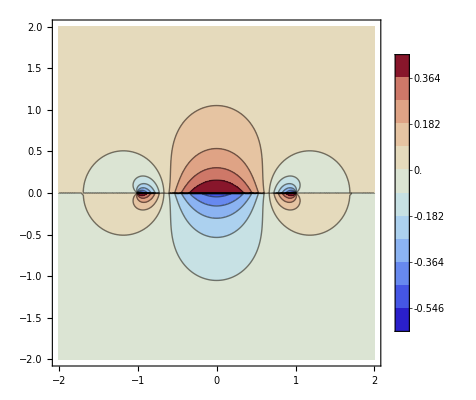

```mathematica
ContourPlot[ReplaceAll[u2,{a->1}],{x,-2,2},{y,-2,2},ColorFunction->"ThermometerColors",PlotLegends->Automatic,PlotRange->Full,PlotPoints->71,Contours->11]
```

### Strain fields

```mathematica
Toplot = D[u2,y]//FullSimplify
ContourPlot[ReplaceAll[Toplot,{a->1}],{x,-2,2},{y,-2,2},ColorFunction->"TemperatureMap",PlotRange->{-2,2},PlotLegends->Automatic,PlotPoints->100,Contours->21]
```

-1/(8 a^2 π)(a (36+(5 a (-a+x))/((a-x)^2+y^2)-(5 a (a+x))/((a+x)^2+y^2))-18 y (ArcTan[(a-x)/y]+ArcTan[(a+x)/y])+9 x Log[(a-x)^2+y^2]-9 x Log[(a+x)^2+y^2])

-Graphics-

## Convert to MATLAB expressions

```mathematica
ToMatlab[u1]
ToMatlab[u2]
ToMatlab[u3]
ex1 = D[u1,x]/2//FullSimplify;
ex2 = D[u2,x]/2//FullSimplify;
ex3 = D[u3,x]/2//FullSimplify;
ey1 = D[u1,y]/2//FullSimplify;
ey2 = D[u2,y]/2//FullSimplify;
ey3 = D[u3,y]/2//FullSimplify;
ToMatlab[ex1]
ToMatlab[ex2]
ToMatlab[ex3]
ToMatlab[ey1]
ToMatlab[ey2]
ToMatlab[ey3]
```

(3/16).*a.^(-2).*pi.^(-1).*(6.*a.*y+((-2).*a.*x+3.*(x+(-1).*y).*( ...
  x+y)).*atan((a+(-1).*x).*y.^(-1))+((-2).*a.*x+3.*(x+(-1).*y).*(x+ ...
  y)).*atan((a+x).*y.^(-1))+(a+(-3).*x).*y.*((-1).*log((a+(-1).*x) ...
  .^2+y.^2)+log((a+x).^2+y.^2)));

(1/8).*a.^(-2).*pi.^(-1).*((-18).*a.*y+(4.*a.^2+9.*y.^2).*atan((a+ ...
  (-1).*x).*y.^(-1))+9.*x.^2.*atan(((-1).*a+x).*y.^(-1))+(4.*a.^2+( ...
  -9).*x.^2+9.*y.^2).*atan((a+x).*y.^(-1))+9.*x.*y.*((-1).*log((a+( ...
  -1).*x).^2+y.^2)+log((a+x).^2+y.^2)));

(3/16).*a.^(-2).*pi.^(-1).*(6.*a.*y+(2.*a.*x+3.*(x+(-1).*y).*(x+y) ...
  ).*atan((a+(-1).*x).*y.^(-1))+(2.*a.*x+3.*(x+(-1).*y).*(x+y)).* ...
  atan((a+x).*y.^(-1))+(a+3.*x).*y.*(log((a+(-1).*x).^2+y.^2)+(-1).* ...
  log((a+x).^2+y.^2)));

(3/32).*a.^(-2).*pi.^(-1).*((-2).*(a+(-3).*x).*(atan((a+(-1).*x).* ...
  y.^(-1))+atan((a+x).*y.^(-1)))+y.*(a.^2.*((-1).*((a+(-1).*x).^2+ ...
  y.^2).^(-1)+5.*((a+x).^2+y.^2).^(-1))+3.*log((a+(-1).*x).^2+y.^2)+ ...
  (-3).*log((a+x).^2+y.^2)));

(1/16).*a.^(-2).*pi.^(-1).*((-18).*x.*(atan((a+(-1).*x).*y.^(-1))+ ...
  atan((a+x).*y.^(-1)))+y.*(20.*a.^3.*x.*(a.^4+2.*a.^2.*((-1).*x.^2+ ...
  y.^2)+(x.^2+y.^2).^2).^(-1)+(-9).*log((a+(-1).*x).^2+y.^2)+9.*log( ...
  (a+x).^2+y.^2)));

(3/32).*a.^(-2).*pi.^(-1).*(2.*(a+3.*x).*(atan((a+(-1).*x).*y.^( ...
  -1))+atan((a+x).*y.^(-1)))+y.*(a.^2.*((-5).*((a+(-1).*x).^2+y.^2) ...
  .^(-1)+((a+x).^2+y.^2).^(-1))+3.*log((a+(-1).*x).^2+y.^2)+(-3).* ...
  log((a+x).^2+y.^2)));

(3/32).*a.^(-2).*pi.^(-1).*(a.*(12+a.*((-1).*a+x).*((a+(-1).*x) ...
  .^2+y.^2).^(-1)+(-5).*a.*(a+x).*((a+x).^2+y.^2).^(-1))+(-6).*y.*( ...
  atan((a+(-1).*x).*y.^(-1))+atan((a+x).*y.^(-1)))+(-1).*(a+(-3).*x) ...
  .*(log((a+(-1).*x).^2+y.^2)+(-1).*log((a+x).^2+y.^2)));

(-1/16).*a.^(-2).*pi.^(-1).*(a.*(36+5.*a.*((-1).*a+x).*((a+(-1).* ...
  x).^2+y.^2).^(-1)+(-5).*a.*(a+x).*((a+x).^2+y.^2).^(-1))+(-18).* ...
  y.*(atan((a+(-1).*x).*y.^(-1))+atan((a+x).*y.^(-1)))+9.*x.*log((a+ ...
  (-1).*x).^2+y.^2)+(-9).*x.*log((a+x).^2+y.^2));

(3/32).*a.^(-2).*pi.^(-1).*(a.*(12+5.*a.*((-1).*a+x).*((a+(-1).*x) ...
  .^2+y.^2).^(-1)+(-1).*a.*(a+x).*((a+x).^2+y.^2).^(-1))+(-6).*y.*( ...
  atan((a+(-1).*x).*y.^(-1))+atan((a+x).*y.^(-1)))+(a+3.*x).*(log(( ...
  a+(-1).*x).^2+y.^2)+(-1).*log((a+x).^2+y.^2)));